```mathematica
ϕ=GoldenRatio//N;
Ψ=1-ϕ//N;
θ=Exp[I*Pi*2/5];
```

```mathematica
Fat[{a_,b_,c_}]:={{a,b,c},"fat"};
Skinny[{a_,b_,c_}]:={{a,b,c},"skinny"};
Coor:=Transpose[{Re/@#,Im/@#}]&;
Cent[{{a_,b_,c_},f_}]:=(a+b)*0.5;
Conj[{{a_,b_,c_},f_}]:={Conjugate/@{a,b,c},f};
AddConj[list_]:=Union[list,Conj/@list];
Cull[l_]:=DeleteDuplicates[l,Cent[#1]==Cent[#2]&];
Rhomb[{{a_,b_,c_},f_}]:={{a,a-c+b,b,c},f};
Δ[{t_,fs_}]:=t;
See:=Graphics[{EdgeForm[Black],Transpose[{Map[If[Last[#]=="fat",Green,Blue]&,#]&@#,Polygon/@Coor/@Δ/@#}]}]&
```

```mathematica
unitfat=Fat[{0,-ϕ,ⅇ^((4 ⅈ π)/5)}];
unitskinny=Fat[{-0.5,0.5,0.5Sqrt[5+2Sqrt[5]]I}];
```

```mathematica
FatInflate[{{a_,b_,c_},f_}]:=
Block[{
d=a+(c-a)/ϕ,
e=a+(b-a)/ϕ},
{Fat[{e,a,d}],Skinny[{d,c,e}],Fat[{b,c,e}]}]

SkinnyInflate[{{a_,b_,c_},s_}]:=
Block[{d=c+(a-c)/ϕ},
{Skinny[{d,a,b}],Fat[{b,c,d}]}]
Inflate:=If[Last[#]=="fat",FatInflate[#],SkinnyInflate[#]]&
```

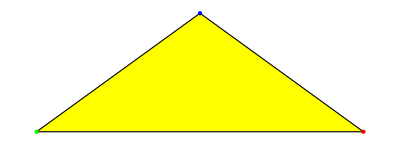

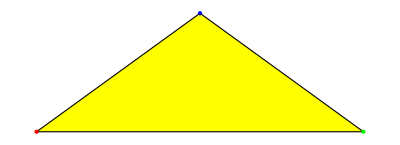
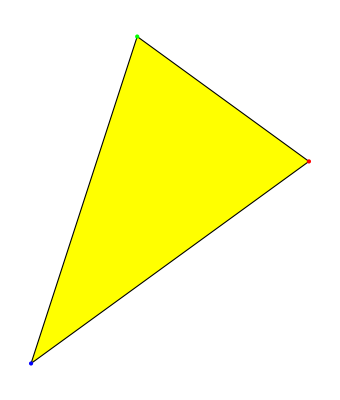
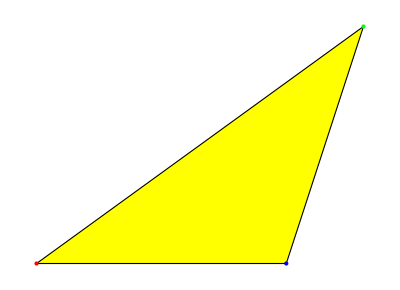

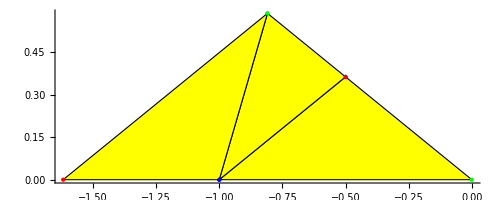

```mathematica
TestPoints@unitfat
TestPoints/@Inflate@unitfat
Show[{TestPoints/@Inflate@unitfat},Axes->True]
```

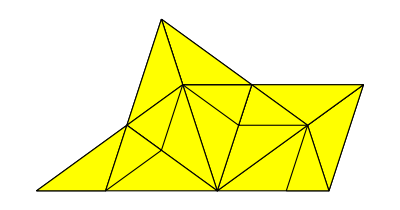

```mathematica
FatInflate/@(Δ/@TriTest);
Δ/@Flatten[%,1];
Coor/@%;
Triangle/@%;
Graphics[{Yellow,EdgeForm[Black],%}]
```

```mathematica
x0=1;
x1=x0*θ;
x2=x1*θ;
y2=-ϕ;
y1=y2/θ;
y0=y1/θ;
TriTest={Fat[{0,y0,x0}],Fat[{0,y0,x1}],Fat[{0,y1,x1}],Fat[{0,y1,x2}],Fat[{0,y2,x2}]};
TriTest1={Fat[0,x0,y0],Fat[0,x1,y0],Fat[0,x1,y1],Fat[0,x2,y1],Fat[0,x2,y2]};
```

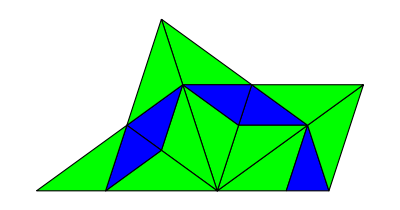

```mathematica
See[Flatten[Inflate/@TriTest,1]]
```

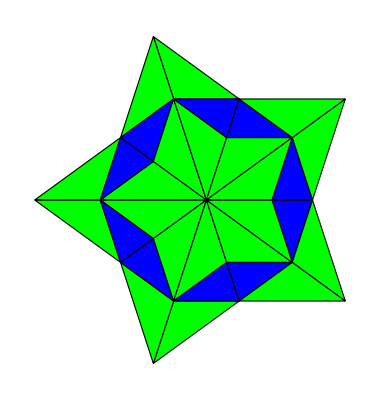

```mathematica
See@AddConj@Flatten[Inflate/@TriTest,1]
```

```mathematica
TestPoints:=Graphics@{Yellow,EdgeForm[Black],{Triangle@Coor@ Δ@#,{PointSize[Large],Transpose[{{Red,Green,Blue},Point/@Coor@Δ@#}]}}}&
```

```mathematica
Inflate[unitfat]
See@Inflate[unitfat]
See@Flatten[Inflate/@Inflate[unitfat],1]
```

```mathematica
Transpose[{Polygon/@Coor/@Δ/@#,Map[If[Last[#]=="fat",Yellow,Blue]&,#]&}]&@Nest[Flatten[Inflate/@#,1]&,{unitfat},3]
```

```mathematica
Transpose[{Polygon/@Coor/@Δ/@#&@Nest[Flatten[Inflate/@#,1]&,{unitfat},3],Map[If[Last[#]=="fat",Yellow,Blue]&,#]&}]@Nest[Flatten[Inflate/@#,1]&,{unitfat},3]
```

```mathematica
Transpose[{Map[If[Last[#]=="fat",Yellow,Blue]&,#]&@#,Polygon/@Coor/@Δ/@#&@#}
]&@Nest[Flatten[Inflate/@#,1]&,{unitfat},3]
```

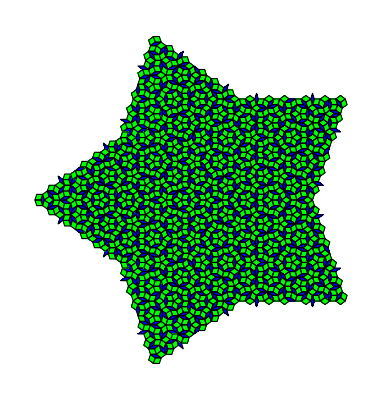

```mathematica
See[Rhomb/@Cull@AddConj@Nest[Flatten[Inflate/@#,1]&,TriTest,6]]
```

{0.,{{{0.517221+0.375783 ⅈ,0.472136+0.343027 ⅈ,0.506578+0.343027 ⅈ},fat},4933,{{-1.+1,1,1},5}}}
 |  |  |  |

{0.,{{{-1.61803,-1.56231,-1.59017-0.0202444 ⅈ},fat},9868,{{1.30902+0.951057 ⅈ,1,19+1},fat}}}
 |  |  |  |

{155.55673,{{{-1.61803,-1.56231,-1.59017-0.0202444 ⅈ},fat},4998,{{1},fat}}}
 |  |  |  |

{159.16697,{{{-1.61803,-1.59017+1,-1.56231,-1.59017-0.0202444 ⅈ},fat},4998,{1}}}
 |  |  |  |

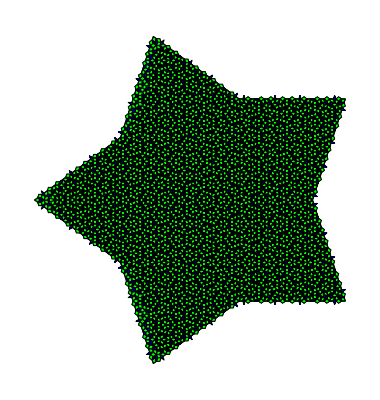
{0.,-Graphics-}

```mathematica
Nest[Flatten[Inflate/@#,1]&,TriTest,7]//Timing
AddConj@Nest[Flatten[Inflate/@#,1]&,TriTest,7]//Timing
Cull@AddConj@Nest[Flatten[Inflate/@#,1]&,TriTest,7]//Timing
Rhomb/@Cull@AddConj@Nest[Flatten[Inflate/@#,1]&,TriTest,7]//Timing
See[Rhomb/@AddConj@Nest[Flatten[Inflate/@#,1]&,TriTest,7]]//Timing
```

```mathematica
See@%
```

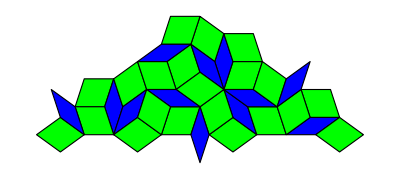

```mathematica
See[Rhomb/@Cull@Nest[Flatten[Inflate/@#,1]&,{unitfat},4]]
```

```mathematica
Graphics[{Yellow,EdgeForm[Black],Polygon/@Coor/@Δ/@#}]&
```

```mathematica
Cull@Nest[Flatten[Inflate/@#,1]&,{unitfat},4]
```

```mathematica
{{-0.5278640450004206,-0.7639320225002102,-0.6458980337503154+0.08575671257690493 ⅈ},"fat"}
```

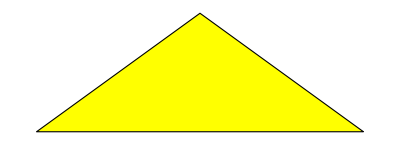

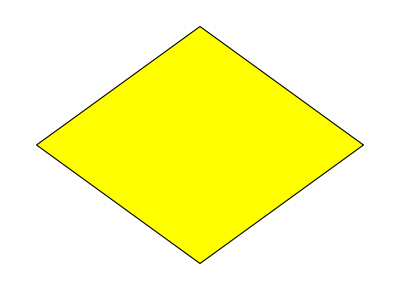

```mathematica
See@{{{-0.5278640450004206,-0.7639320225002102,-0.6458980337503154+0.08575671257690493 ⅈ},"fat"}}
See@{Rhomb@{{-0.5278640450004206,-0.7639320225002102,-0.6458980337503154+0.08575671257690493 ⅈ},"fat"}}
```

{{0,-1.61803,ⅇ^((4 ⅈ π)/5)},fat}

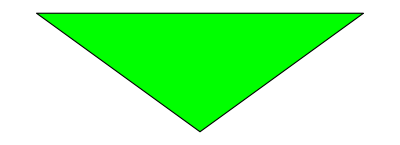

```mathematica
unitfat
See@{Conj[unitfat]}
```

```mathematica
Transpose[{(Δ/@#),Cent/@#}]&@Nest[Flatten[Inflate/@#,1]&,TriTest,3]
```

{{{0.618034+0.449028 ⅈ,0.309017+0.224514 ⅈ,0.545085+0.224514 ⅈ},0.463525+0.336771 ⅈ},{{0.545085+0.224514 ⅈ,0.690983+0.224514 ⅈ,0.618034+0.449028 ⅈ},0.618034+0.224514 ⅈ},{{0.809017+0.587785 ⅈ,0.690983+0.224514 ⅈ,0.618034+0.449028 ⅈ},0.75+0.40615 ⅈ},{{0.545085+0.224514 ⅈ,0.690983+0.224514 ⅈ,0.618034},0.618034+0.224514 ⅈ},{{0.618034,0.309017+0.224514 ⅈ,0.545085+0.224514 ⅈ},0.463525+0.112257 ⅈ},{{0.381966,0,0.190983+0.138757 ⅈ},0.190983},{{0.190983+0.138757 ⅈ,0.309017+0.224514 ⅈ,0.381966},0.25+0.181636 ⅈ},{{0.618034,0.309017+0.224514 ⅈ,0.381966},0.463525+0.112257 ⅈ},{{0.809017+0.138757 ⅈ,0.690983+0.224514 ⅈ,0.618034},0.75+0.181636 ⅈ},{{0.618034,1,0.809017+0.138757 ⅈ},0.809017},{{0.881966+0.363271 ⅈ,1,0.809017+0.138757 ⅈ},0.940983+0.181636 ⅈ},{{0.809017+0.138757 ⅈ,0.690983+0.224514 ⅈ,0.881966+0.363271 ⅈ},0.75+0.181636 ⅈ},{{0.809017+0.587785 ⅈ,0.690983+0.224514 ⅈ,0.881966+0.363271 ⅈ},0.75+0.40615 ⅈ},{{1.23607+0.726543 ⅈ,1.11803+0.363271 ⅈ,1.04508+0.587785 ⅈ},1.17705+0.544907 ⅈ},{{1.04508+0.587785 ⅈ,1.+0.726543 ⅈ,1.23607+0.726543 ⅈ},1.02254+0.657164 ⅈ},{{1.30902+0.951057 ⅈ,1.+0.726543 ⅈ,1.23607+0.726543 ⅈ},1.15451+0.8388 ⅈ},{{1.04508+0.587785 ⅈ,1.+0.726543 ⅈ,0.809017+0.587785 ⅈ},1.02254+0.657164 ⅈ},{{0.809017+0.587785 ⅈ,1.11803+0.363271 ⅈ,1.04508+0.587785 ⅈ},0.963525+0.475528 ⅈ},{{0.881966+0.363271 ⅈ,1,1.07295+0.224514 ⅈ},0.940983+0.181636 ⅈ},{{1.07295+0.224514 ⅈ,1.11803+0.363271 ⅈ,0.881966+0.363271 ⅈ},1.09549+0.293893 ⅈ},{{0.809017+0.587785 ⅈ,1.11803+0.363271 ⅈ,0.881966+0.363271 ⅈ},0.963525+0.475528 ⅈ},{{0.618034+0.449028 ⅈ,0.309017+0.224514 ⅈ,0.381966+0.449028 ⅈ},0.463525+0.336771 ⅈ},{{0.381966+0.449028 ⅈ,0.427051+0.587785 ⅈ,0.618034+0.449028 ⅈ},0.404508+0.518407 ⅈ},{{0.809017+0.587785 ⅈ,0.427051+0.587785 ⅈ,0.618034+0.449028 ⅈ},0.618034+0.587785 ⅈ},{{0.381966+0.449028 ⅈ,0.427051+0.587785 ⅈ,0.190983+0.587785 ⅈ},0.404508+0.518407 ⅈ},{{0.190983+0.587785 ⅈ,0.309017+0.224514 ⅈ,0.381966+0.449028 ⅈ},0.25+0.40615 ⅈ},{{0.118034+0.363271 ⅈ,0,0.190983+0.138757 ⅈ},0.059017+0.181636 ⅈ},{{0.190983+0.138757 ⅈ,0.309017+0.224514 ⅈ,0.118034+0.363271 ⅈ},0.25+0.181636 ⅈ},{{0.190983+0.587785 ⅈ,0.309017+0.224514 ⅈ,0.118034+0.363271 ⅈ},0.25+0.40615 ⅈ},{{0.381966+0.726543 ⅈ,0.427051+0.587785 ⅈ,0.190983+0.587785 ⅈ},0.404508+0.657164 ⅈ},{{0.190983+0.587785 ⅈ,ⅇ^((2 ⅈ π)/5),0.381966+0.726543 ⅈ},0.25+0.769421 ⅈ},{{0.618034+0.726543 ⅈ,ⅇ^((2 ⅈ π)/5),0.381966+0.726543 ⅈ},0.463525+0.8388 ⅈ},{{0.381966+0.726543 ⅈ,0.427051+0.587785 ⅈ,0.618034+0.726543 ⅈ},0.404508+0.657164 ⅈ},{{0.809017+0.587785 ⅈ,0.427051+0.587785 ⅈ,0.618034+0.726543 ⅈ},0.618034+0.587785 ⅈ},{{1.07295+0.951057 ⅈ,0.690983+0.951057 ⅈ,0.881966+0.812299 ⅈ},0.881966+0.951057 ⅈ},{{0.881966+0.812299 ⅈ,1.+0.726543 ⅈ,1.07295+0.951057 ⅈ},0.940983+0.769421 ⅈ},{{1.30902+0.951057 ⅈ,1.+0.726543 ⅈ,1.07295+0.951057 ⅈ},1.15451+0.8388 ⅈ},{{0.881966+0.812299 ⅈ,1.+0.726543 ⅈ,0.809017+0.587785 ⅈ},0.940983+0.769421 ⅈ},{{0.809017+0.587785 ⅈ,0.690983+0.951057 ⅈ,0.881966+0.812299 ⅈ},0.75+0.769421 ⅈ},{{0.618034+0.726543 ⅈ,ⅇ^((2 ⅈ π)/5),0.545085+0.951057 ⅈ},0.463525+0.8388 ⅈ},{{0.545085+0.951057 ⅈ,0.690983+0.951057 ⅈ,0.618034+0.726543 ⅈ},0.618034+0.951057 ⅈ},{{0.809017+0.587785 ⅈ,0.690983+0.951057 ⅈ,0.618034+0.726543 ⅈ},0.75+0.769421 ⅈ},{{-0.236068+0.726543 ⅈ,-0.118034+0.363271 ⅈ,-0.045085+0.587785 ⅈ},-0.177051+0.544907 ⅈ},{{-0.045085+0.587785 ⅈ,-5.55112×10^-17+0.726543 ⅈ,-0.236068+0.726543 ⅈ},-0.0225425+0.657164 ⅈ},{{-0.309017+0.951057 ⅈ,-5.55112×10^-17+0.726543 ⅈ,-0.236068+0.726543 ⅈ},-0.154508+0.8388 ⅈ},{{-0.045085+0.587785 ⅈ,-5.55112×10^-17+0.726543 ⅈ,0.190983+0.587785 ⅈ},-0.0225425+0.657164 ⅈ},{{0.190983+0.587785 ⅈ,-0.118034+0.363271 ⅈ,-0.045085+0.587785 ⅈ},0.0364745+0.475528 ⅈ},{{0.118034+0.363271 ⅈ,0,-0.072949+0.224514 ⅈ},0.059017+0.181636 ⅈ},{{-0.072949+0.224514 ⅈ,-0.118034+0.363271 ⅈ,0.118034+0.363271 ⅈ},-0.0954915+0.293893 ⅈ},{{0.190983+0.587785 ⅈ,-0.118034+0.363271 ⅈ,0.118034+0.363271 ⅈ},0.0364745+0.475528 ⅈ},{{0.118034+0.812299 ⅈ,-5.55112×10^-17+0.726543 ⅈ,0.190983+0.587785 ⅈ},0.059017+0.769421 ⅈ},{{0.190983+0.587785 ⅈ,ⅇ^((2 ⅈ π)/5),0.118034+0.812299 ⅈ},0.25+0.769421 ⅈ},{{-0.072949+0.951057 ⅈ,ⅇ^((2 ⅈ π)/5),0.118034+0.812299 ⅈ},0.118034+0.951057 ⅈ},{{0.118034+0.812299 ⅈ,-5.55112×10^-17+0.726543 ⅈ,-0.072949+0.951057 ⅈ},0.059017+0.769421 ⅈ},{{-0.309017+0.951057 ⅈ,-5.55112×10^-17+0.726543 ⅈ,-0.072949+0.951057 ⅈ},-0.154508+0.8388 ⅈ},{{-0.309017+1.40008 ⅈ,-1.11022×10^-16+1.17557 ⅈ,-0.236068+1.17557 ⅈ},-0.154508+1.28783 ⅈ},{{-0.236068+1.17557 ⅈ,-0.381966+1.17557 ⅈ,-0.309017+1.40008 ⅈ},-0.309017+1.17557 ⅈ},{{-0.5+1.53884 ⅈ,-0.381966+1.17557 ⅈ,-0.309017+1.40008 ⅈ},-0.440983+1.35721 ⅈ},{{-0.236068+1.17557 ⅈ,-0.381966+1.17557 ⅈ,-0.309017+0.951057 ⅈ},-0.309017+1.17557 ⅈ},{{-0.309017+0.951057 ⅈ,-1.11022×10^-16+1.17557 ⅈ,-0.236068+1.17557 ⅈ},-0.154508+1.06331 ⅈ},{{-0.072949+0.951057 ⅈ,ⅇ^((2 ⅈ π)/5),0.118034+1.08981 ⅈ},0.118034+0.951057 ⅈ},{{0.118034+1.08981 ⅈ,-1.11022×10^-16+1.17557 ⅈ,-0.072949+0.951057 ⅈ},0.059017+1.13269 ⅈ},{{-0.309017+0.951057 ⅈ,-1.11022×10^-16+1.17557 ⅈ,-0.072949+0.951057 ⅈ},-0.154508+1.06331 ⅈ},{{-0.236068+0.726543 ⅈ,-0.118034+0.363271 ⅈ,-0.309017+0.502029 ⅈ},-0.177051+0.544907 ⅈ},{{-0.309017+0.502029 ⅈ,-0.427051+0.587785 ⅈ,-0.236068+0.726543 ⅈ},-0.368034+0.544907 ⅈ},{{-0.309017+0.951057 ⅈ,-0.427051+0.587785 ⅈ,-0.236068+0.726543 ⅈ},-0.368034+0.769421 ⅈ},{{-0.309017+0.502029 ⅈ,-0.427051+0.587785 ⅈ,-0.5+0.363271 ⅈ},-0.368034+0.544907 ⅈ},{{-0.5+0.363271 ⅈ,-0.118034+0.363271 ⅈ,-0.309017+0.502029 ⅈ},-0.309017+0.363271 ⅈ},{{-0.309017+0.224514 ⅈ,0,-0.072949+0.224514 ⅈ},-0.154508+0.112257 ⅈ},{{-0.072949+0.224514 ⅈ,-0.118034+0.363271 ⅈ,-0.309017+0.224514 ⅈ},-0.0954915+0.293893 ⅈ},{{-0.5+0.363271 ⅈ,-0.118034+0.363271 ⅈ,-0.309017+0.224514 ⅈ},-0.309017+0.363271 ⅈ},{{-0.572949+0.587785 ⅈ,-0.427051+0.587785 ⅈ,-0.5+0.363271 ⅈ},-0.5+0.587785 ⅈ},{{-0.5+0.363271 ⅈ,ⅇ^((4 ⅈ π)/5),-0.572949+0.587785 ⅈ},-0.654508+0.475528 ⅈ},{{-0.5+0.812299 ⅈ,ⅇ^((4 ⅈ π)/5),-0.572949+0.587785 ⅈ},-0.654508+0.700042 ⅈ},{{-0.572949+0.587785 ⅈ,-0.427051+0.587785 ⅈ,-0.5+0.812299 ⅈ},-0.5+0.587785 ⅈ},{{-0.309017+0.951057 ⅈ,-0.427051+0.587785 ⅈ,-0.5+0.812299 ⅈ},-0.368034+0.769421 ⅈ},{{-0.572949+1.31433 ⅈ,-0.690983+0.951057 ⅈ,-0.5+1.08981 ⅈ},-0.631966+1.13269 ⅈ},{{-0.5+1.08981 ⅈ,-0.381966+1.17557 ⅈ,-0.572949+1.31433 ⅈ},-0.440983+1.13269 ⅈ},{{-0.5+1.53884 ⅈ,-0.381966+1.17557 ⅈ,-0.572949+1.31433 ⅈ},-0.440983+1.35721 ⅈ},{{-0.5+1.08981 ⅈ,-0.381966+1.17557 ⅈ,-0.309017+0.951057 ⅈ},-0.440983+1.13269 ⅈ},{{-0.309017+0.951057 ⅈ,-0.690983+0.951057 ⅈ,-0.5+1.08981 ⅈ},-0.5+0.951057 ⅈ},{{-0.5+0.812299 ⅈ,ⅇ^((4 ⅈ π)/5),-0.736068+0.812299 ⅈ},-0.654508+0.700042 ⅈ},{{-0.736068+0.812299 ⅈ,-0.690983+0.951057 ⅈ,-0.5+0.812299 ⅈ},-0.713525+0.881678 ⅈ},{{-0.309017+0.951057 ⅈ,-0.690983+0.951057 ⅈ,-0.5+0.812299 ⅈ},-0.5+0.951057 ⅈ},{{-0.763932,-0.381966,-0.572949+0.138757 ⅈ},-0.572949},{{-0.572949+0.138757 ⅈ,-0.690983+0.224514 ⅈ,-0.763932},-0.631966+0.181636 ⅈ},{{-1.,-0.690983+0.224514 ⅈ,-0.763932},-0.845492+0.112257 ⅈ},{{-0.572949+0.138757 ⅈ,-0.690983+0.224514 ⅈ,-0.5+0.363271 ⅈ},-0.631966+0.181636 ⅈ},{{-0.5+0.363271 ⅈ,-0.381966,-0.572949+0.138757 ⅈ},-0.440983+0.181636 ⅈ},{{-0.309017+0.224514 ⅈ,0,-0.236068},-0.154508+0.112257 ⅈ},{{-0.236068,-0.381966,-0.309017+0.224514 ⅈ},-0.309017},{{-0.5+0.363271 ⅈ,-0.381966,-0.309017+0.224514 ⅈ},-0.440983+0.181636 ⅈ},{{-0.736068+0.363271 ⅈ,-0.690983+0.224514 ⅈ,-0.5+0.363271 ⅈ},-0.713525+0.293893 ⅈ},{{-0.5+0.363271 ⅈ,ⅇ^((4 ⅈ π)/5),-0.736068+0.363271 ⅈ},-0.654508+0.475528 ⅈ},{{-0.927051+0.224514 ⅈ,ⅇ^((4 ⅈ π)/5),-0.736068+0.363271 ⅈ},-0.868034+0.40615 ⅈ},{{-0.736068+0.363271 ⅈ,-0.690983+0.224514 ⅈ,-0.927051+0.224514 ⅈ},-0.713525+0.293893 ⅈ},{{-1.,-0.690983+0.224514 ⅈ,-0.927051+0.224514 ⅈ},-0.845492+0.112257 ⅈ},{{-1.42705+0.138757 ⅈ,-1.11803+0.363271 ⅈ,-1.19098+0.138757 ⅈ},-1.27254+0.251014 ⅈ},{{-1.19098+0.138757 ⅈ,-1.23607,-1.42705+0.138757 ⅈ},-1.21353+0.0693786 ⅈ},{{-1.61803,-1.23607,-1.42705+0.138757 ⅈ},-1.42705},{{-1.19098+0.138757 ⅈ,-1.23607,-1.},-1.21353+0.0693786 ⅈ},{{-1.,-1.11803+0.363271 ⅈ,-1.19098+0.138757 ⅈ},-1.05902+0.181636 ⅈ},{{-0.927051+0.224514 ⅈ,ⅇ^((4 ⅈ π)/5),-1.+0.449028 ⅈ},-0.868034+0.40615 ⅈ},{{-1.+0.449028 ⅈ,-1.11803+0.363271 ⅈ,-0.927051+0.224514 ⅈ},-1.05902+0.40615 ⅈ},{{-1.,-1.11803+0.363271 ⅈ,-0.927051+0.224514 ⅈ},-1.05902+0.181636 ⅈ}}